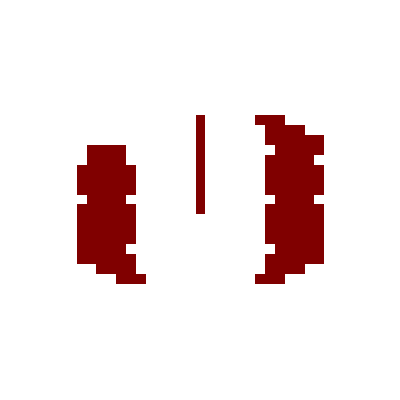

```mathematica
p[z_]=(z^2-1)(z-λ); lp[z_]=p[z]p''[z]/p'[z]/p'[z];sp[z_]=z-1/(1-lp[z])p[z]/p'[z]; soluciones=Solve[-2 (λ+λ^3)+(3+9 λ^2) z-12 λ z^2+(3+λ^2) z^3==0,z];
r0=1.;r1=-1.;r2=λ;
rootPosition := Compile[{{z,_Complex}},
    Which[Abs[z -r0] <  10.0^(-6),1,
Abs[z-r1]<10.0^(-6), 1,
Abs[z-r2]<10.0^(-6), 1,
    True, 0],
{{rootf[_],_Complex}}
]
iterSchLambda = Compile[{{z, _Complex},{ λ,_Complex}},(4 z^3+λ-10 z^2 λ+z^4 λ+4 z λ^2)/(1+3 z^4-4 z λ-4 z^3 λ+2 λ^2+2 z^2 λ^2)];
iterColorAlgorithm[iterMethod_,x_,y_,lim_] :=
    Block[{z,λ,ct,r}, z =z/.soluciones[[3]];
λ= x + y I; ct = 0;r = rootPosition[z];
raiz1=0;
        While[(r==0) && (ct < lim),
            ++ct; z = iterMethod[z,λ];r = rootPosition[z]
	       ];
		    If[r==1,raiz1=1];
		  
z =z/.soluciones[[2]];λ= x + y I; ct = 0;r = rootPosition[z];
     raiz2=0   ;
While[(r==0) && (ct < lim),
            ++ct; z = iterMethod[z,λ];r = rootPosition[z]
	       ];
		    If[r==1,raiz2=1];
z =z/.soluciones[[1]];λ= x + y I; ct = 0;r = rootPosition[z];
     raiz3=0;  
 While[(r==0) && (ct < lim),
            ++ct; z = iterMethod[z,λ];r = rootPosition[z]
	       ];
		    If[r==1,raiz3=1]; (* "Which" unevaluated Return[N[r+ct/(lim+0.001)]] *)
	Return[N[raiz3*4+raiz2*2+raiz1]]

    ]
Clear[fractalColorWS]

ft[min_,max_,pt_,nTicks_]:=Block[{taux,j,stepTicks=(max-min)/(nTicks-1)},
taux=Table[{pt*(j-1)/(nTicks-1)+1,min+(j-1)*stepTicks},{j,1,nTicks}]
]
Clear[plotColorFractal]
plotColorFractal[iterMethod_,points_]:=
Block[{$Messages = {},
stepx=(xxMax-xxMin)/points,stepy=(yyMax-yyMin)/points},
ArrayPlot[Table[iterColorAlgorithm[iterMethod,x,y,limIterations],
{y,yyMax,1.00001*yyMin,-stepy},
{x,xxMin,1.00001*xxMax,stepx}],
FrameTicks->{ft[yyMax,yyMin,points,5],ft[xxMin,xxMax,points,5]},
PlotRange->{0,5},(* Three roots + fixed  *)
ColorFunctionScaling->False,
ColorFunction->fractalColorWS
]
]
Off[General::ovfl];    Off[General::unfl];    Off[Infinity::indet]
Off[CompiledFunction::cccx];    Off[CompiledFunction::cfn]; Off[CompiledFunction::cfcx];    Off[CompiledFunction::cfex]; Off[CompiledFunction::crcx];    Off[CompiledFunction::cfse]; Off[CompiledFunction::ilsm];    Off[CompiledFunction::cfsa]
numberPoints =32;limIterations=100;
xxMin=-5.25; xxMax=5.25; yyMin=-3.4; yyMax=3.4;plotColorFractal[iterSchLambda, numberPoints]
```